# Practical 1

## Solve the first order ordinary differential equations

### First order ordinary differential equations: The differential equations that involves the first order derivatives of dependent variable with respect to independent variable Command: DSolve[Differential Equation, y[x], x]

### Q1 dy/dx + y = 0

1. Solve the first order differential equation dy/dx + y = 0

```mathematica
S1= DSolve[y'[x]+y[x]==0, y[x], x]
```

{{y[x]→ⅇ^-x C[1]}}

2. Solve the above differential equation using the initial condition: y(0) = 2

```mathematica
S2 = Evaluate[y[x]/.S1[[1]]/.C[1]->2]
```

2 ⅇ^-x

3. Solve the above differential equation using the initial condition: y(0) = 1, 2 and 4 and Plot them

```mathematica
S3 = Evaluate[y[x]/.S1[[1]]/.C[1]->{1, 2, 4}]
```

{ⅇ^-x,2 ⅇ^-x,4 ⅇ^-x}

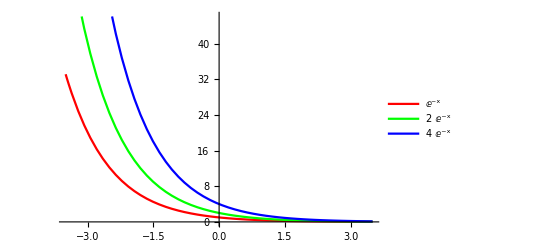

```mathematica
Plot[S3, {x, -3.5, 3.5}, PlotStyle->{{Red, Thick}, {Green, Thick}, {Blue, Thick}}, PlotLegends->S3]
```

### Q2 dy/dx - y^2= 0

1. Solve the first order differential equation dy/dx - y^2 = 0

```mathematica
S1= DSolve[y'[x]- y[x]^2==0, y[x], x]
```

{{y[x]→1/(-x-C[1])}}

2. Solve the above differential equation using the initial condition: y(0) = 1

```mathematica
S2 = Evaluate[y[x]/.S1[[1]]/.C[1]->1]
```

1/(-1-x)

3. Solve the above differential equation using the initial condition: y(0) = 1, 2 and 4 and Plot them

```mathematica
S3 = Evaluate[y[x]/.S1[[1]]/.C[1]->{1, 2, 4}]
```

{1/(-1-x),1/(-2-x),1/(-4-x)}

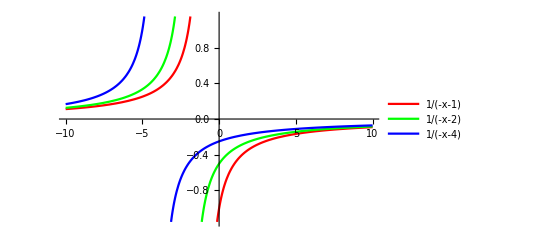

```mathematica
Plot[S3, {x, -10, 10}, PlotStyle->{{Red, Thick}, {Green, Thick}, {Blue, Thick}}, PlotLegends->S3]
```